```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,500,550,575,600};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

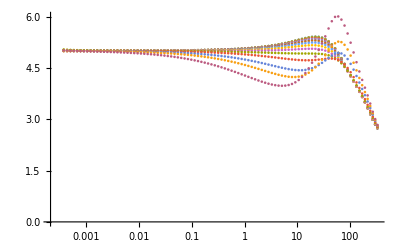

```mathematica
ListPlot[fitdata,PlotRange->All,ScalingFunctions->{"Log"}]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
T0p01=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-5)/5]==0.01,{x,0.01,0.001,40}],2][[1]][[2]],{i,1,Length[mub]}]
Export["../../2D_phase_plot/delta0p01.dat",T0p01];
T0p02=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-5)/5]==0.02,{x,0.1,0.001,40}],2][[1]][[2]],{i,1,Length[mub]}]
Export["../../2D_phase_plot/delta0p02.dat",T0p02];
T0p03=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-5)/5]==0.03,{x,0.8,0.001,50}],2][[1]][[2]],{i,1,Length[mub]}]
Export["../../2D_phase_plot/delta0p03.dat",T0p03];
```

{0.590649,0.598944,0.625961,0.678543,0.773322,0.951981,1.3446,2.54235,11.414,2.08352,0.25237,0.0481776,0.018054,0.00509723}

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

{1.70885,1.73175,1.80562,1.94837,2.20286,2.67466,3.6798,6.6281,18.0888,31.0539,0.925543,0.167908,0.0620902,0.0166705}

FindRoot::reged: 点 {50.} 位于搜索区域 {0.001,50.} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

{3.13011,3.1715,3.30482,3.56237,4.02167,4.87637,6.73344,13.386,50.,42.0125,2.10064,0.357484,0.130995,0.0347935}